## Functions for modeling

UNITS:
	cij: GPa;
	x: km;
	t: s;
	k: 1/m

### Linear-solid stiffness matrix

cij0[i], Q0[i] are assumed defined for each layer i

```mathematica
cijCarcione[pars_,ω0_,ω_]:=Module[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},

{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i}=pars;

{(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c33i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c11i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),c13i-(2 c44i ω ((-2+√(1+Q01i^2)+√(1+Q02i^2)) ω+ⅈ (Q01i+Q02i) ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))+c11i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω)+c33i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω),(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c11i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c33i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),(c44i (ω+√(1+Q02i^2) ω+ⅈ Q02i ω0))/((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0),ρi}//N

]
```

```mathematica
cijCarcioneCompiled=
Compile[{{cijQρ,_Real, 1},{ω0,_Real},{ω,_Complex}},
Module[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},

c11i=cijQρ[[1]];
c13i=cijQρ[[2]];
c33i=cijQρ[[3]];
c44i=cijQρ[[4]];
ρi=cijQρ[[5]];
Q01i=cijQρ[[6]];
Q02i=cijQρ[[7]];

{(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c33i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c11i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),c13i-(2 c44i ω ((-2+√(1+Q01i^2)+√(1+Q02i^2)) ω+ⅈ (Q01i+Q02i) ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))+c11i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω)+c33i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω),(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c11i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c33i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),(c44i (ω+√(1+Q02i^2) ω+ⅈ Q02i ω0))/((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0),Re@ρi}

],CompilationTarget->"C", RuntimeOptions->"Speed"
];
```

```mathematica
cijLS[{c11i_,c13i_,c33i_,c44i_,ρi_,Q01i_,Q02i_},ω0_,ω_]:=cijCarcioneCompiled[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},ω0,ω];
```

### Slowness, L1/L2 matrices

Requires run of the cijCarcione function to get frequency-dependent cij[i]

```mathematica
GetLStovasUrsin[{c11i_, c13i_, c33i_, c44i_, ρi_},p_]:=Module[
{L1,L2,d1,d2,d3,d4,d5,qα,qβ,α0,β0,η,δ,σ0,Sα,Sβ,R,R1,R2,req1,req2,imq1,imq2},
α0=√(c33i/ρi);
β0=√(c44i/ρi);
σ0=1-c44i/c33i;
δ=(c13i-c33i+2c44i)/c33i;
η=(c11i c33i-(c13i+2c44i)^2)/(2 c33i^2);
R1=2(1-p^2 β0^2)(δ+2 p^2 α0^2 η)^2;
R2=σ0+2 p^2 β0^2 δ-2 p^2 α0^2(1-2 p^2 β0^2)η;
R=R1/(R2+√(R2^2+2 p^2 β0^2 R1));
Sα=2δ+2 p^2 α0^2 η+R;
Sβ=2(1-p^2 β0^2)α0^2/β0^2 η-R;

d2=√((σ0+δ)/(σ0+Sα));
d3=2 β0^2(σ0+1/2(Sα+δ))/(σ0+δ);
d4=√((σ0-p^2 β0^2(σ0+Sβ))/((1-p^2 β0^2(1+Sβ))(σ0+δ)));
d5=(σ0-2 p^2 β0^2(σ0+1/2(Sβ+δ)))/(σ0+δ);
d1=1/(√(p^2 d3+d5));


qα=(Re@#+ⅈ Abs@Im@#)&@√(1/α0^2-p^2-p^2 Sα);
qβ=(Re@#+ⅈ Abs@Im@#)&@√(1/β0^2-p^2-p^2 Sβ);

(*qα=1/α0^2-p^2-p^2 Sα;
qβ=1/β0^2-p^2-p^2 Sβ;*)
(*
qα=Sign[Im[qα]]qα;
qβ=Sign[Im[qβ]]qβ;*)



L1=d1{
{d2 √(qα/ρi),1/d4 p/(√(ρi qβ))},
{d3 d2 p √(ρi qα),-d5/d4 √(ρi/qβ)}
};

L2=d1{
{d5/d2 √(ρi/qα),d3 d4 p √(ρi qβ)},
{1/d2 p/(√(ρi qα)),-d4 √(qβ/ρi)}
};

(*{{qα,qβ},{L1,L2}}*)
{{{qα,0},{0,qβ}},L1,L2}
(*l1[j]=L1//N;
l2[j]=L2//N;
q1[j]=qα//N;
q2[j]=qβ//N;*)

]
```

```mathematica
qLCompiled=
Compile[{{cij,_Complex, 1},{ρi,_Real},{p,_Complex}},
Module[
{L1,L2,d1,d2,d3,d4,d5,qα,qβ,α0,β0,η,δ,σ0,Sα,Sβ,R,R1,R2},
α0=√(cij[[3]]/ρi);
β0=√(cij[[4]]/ρi);
σ0=1-cij[[4]]/cij[[3]];
δ=(cij[[2]]-cij[[3]]+2cij[[4]])/cij[[3]];
η=(cij[[1]] cij[[3]]-(cij[[2]]+2cij[[4]])^2)/(2 cij[[3]]^2);
R1=2(1-p^2 β0^2)(δ+2 p^2 α0^2 η)^2;
R2=σ0+2 p^2 β0^2 δ-2 p^2 α0^2(1-2 p^2 β0^2)η;
R=R1/(R2+√(R2^2+2 p^2 β0^2 R1));
Sα=2δ+2 p^2 α0^2 η+R;
Sβ=2(1-p^2 β0^2)α0^2/β0^2 η-R;

qα=(Re@#+ⅈ Abs@Im@#)&@√(1/α0^2-p^2-p^2 Sα);
qβ=(Re@#+ⅈ Abs@Im@#)&@√(1/β0^2-p^2-p^2 Sβ);
d2=√((σ0+δ)/(σ0+Sα));
d3=2 β0^2(σ0+1/2(Sα+δ))/(σ0+δ);
d4=√((σ0-p^2 β0^2(σ0+Sβ))/((1-p^2 β0^2(1+Sβ))(σ0+δ)));
d5=(σ0-2 p^2 β0^2(σ0+1/2(Sβ+δ)))/(σ0+δ);
d1=1/(√(p^2 d3+d5));
L1=d1{
{d2 √(qα/ρi),1/d4 p/(√(ρi qβ))},
{d3 d2 p √(ρi qα),-d5/d4 √(ρi/qβ)}
};

L2=d1{
{d5/d2 √(ρi/qα),d3 d4 p √(ρi qβ)},
{1/d2 p/(√(ρi qα)),-d4 √(qβ/ρi)}
};

{{{qα,0},{0,qβ}},L1,L2}
],CompilationTarget->"C", RuntimeOptions->"Speed"
];
```

```mathematica
qL[{c11i_, c13i_, c33i_, c44i_, ρi_},p_]:=qLCompiled[{c11i, c13i, c33i, c44i}, ρi,p];
```

### Reflectivity and transmissivity

```mathematica
(*
REFLECTIVITY ONLY -- source/receiver depth included
*)
stackRefExperiment2[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List,{zs_,zr_}]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray, L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f,exp},

{qABArray, L1ar, L2ar}=Transpose[qL[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
exp[z_]:=Exp[ⅈ ω z qABArray[[1]]]-{{0,1},{1,0}};
exp[zr].Fold[f[#1,#2⟦1⟧,#2⟦2⟧,#2⟦3⟧]&,{{0,0},{0,0}},foldArray].exp[zs]
(*;
{transArray,refArray, phaseArray}*)
(*foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}]*)
(*;
phaseArray=Exp[ⅈ ω(qABArray d)];
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}]*)
]
```

```mathematica
(*
BOTH REFLECTIVITY AND TRANSMISSIVITY
OUPUT[[1]] IS TRANSMISSIVITY MATRIX
OUPUT[[2]] IS REFLECTIVITY MATRIX
*)
stackRefExperiment2RT[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray, L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,fR,fT},
{qABArray, L1ar, L2ar}=Transpose[qL[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
fR=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
fT=(#1.Inverse[IdentityMatrix[2]+#3.fR[#5,#2,#3,#4]].#2.#4)&;
Fold[
{fT[#1[[1]],#2[[1]],#2[[2]],#2[[3]],#1[[2]]],
fR[#1[[2]],#2[[1]],#2[[2]],#2[[3]]]}&,{{{1,0},{0,1}},{{0,0},{0,0}}},foldArray]
]
```

```mathematica
<<CompiledFunctionTools`
```

```mathematica
stackRefExperiment[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray,L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L1ar, L2ar}=Transpose[GetLStovasUrsin[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray]
]
```

```mathematica
stackRefTransCoefs[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray,L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L1ar, L2ar}=Transpose[GetLStovasUrsin[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
CArray=MapThread[Transpose[#1].#2&,{RotateLeft@L12Array[[;;,2]],L12Array[[;;,1]]}];
DArray=MapThread[Transpose[#1].#2&,{RotateLeft@L12Array[[;;,1]],L12Array[[;;,2]]}];
transArray=2Transpose/@ Inverse/@(CArray+DArray);
refArray=1/2 MapThread[#1.#2&,{Transpose/@(CArray-DArray),transArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray]
]
```

### Time-domain description

```mathematica
(*
NOTE THAT RPP IS TAKEN FOR INTEGRATION ([[1,1]] after the StackRefExperiment function)
*)
addSrcRec[RT_,ω_,zs_,zr_,qAB1_]:=Module[
{exp},

exp[z_]:=Exp[ⅈ ω z qAB1]-{{0,1},{1,0}};

exp[zr].RT.exp[zs]//N//Chop

]

integrandp[x_,p_?NumericQ,ω_?NumericQ,CijsAndρ:{{_,_,_,_,_}..},dList_,zs_,zr_]:=With[{p0=p},
stackRefExperiment2[ω,p0,CijsAndρ, dList,{zs,zr}][[1,1]] BesselJ[0,x p0 ω]p0 ω^2]

integrandk[x_,k_?NumericQ,ω_?NumericQ,CijsAndρ:{{_,_,_,_,_}..},dList_,zs_,zr_]:=With[{k0=1000k},
stackRefExperiment2[ω,k0/ω,CijsAndρ, dList,{zs,zr}][[1,1]] BesselJ[0,x k0]k0]

integrandkFullDisp[x_,k_?NumericQ,ω_?NumericQ,CijsAndρ:{{_,_,_,_,_}..},dList_,zs_,zr_,{i_,j_}]:=With[{k0=1000k},
stackRefExperiment2[ω,k0/ω,CijsAndρ, dList,{zs,zr}][[i,j]] BesselJ[0,x k0] k0/(ⅈ ω)]

integrandkFourier[x_,k_?NumericQ,ω_?NumericQ,CijsAndρ:{{_,_,_,_,_}..},dList_,zs_,zr_]:=With[{k0=1000k},
stackRefExperiment2[ω,k0/ω,CijsAndρ, dList,{zs,zr}][[1,1]] Exp[ⅈ x k0]]

(*VARIABLE UPPER BOUNDARY FOR INTEGRATION*)
upperB[f_,fm_,p0_,pm_]:=p0+f/fm pm
rickerF[f_,fp_]:=Module[{ω=2Pi f,ωp=2Pi fp},(2 ω^2)/(√Pi ωp^3)Exp[-(ω/ωp)^2]//N]
integrateNow[f_,offset_,{zs_,zr_},maxfreq_,model_,dList_,ω0_,{slope0_,slopeEnd_}]:=Module[{ωc=2Pi f},
NIntegrate[
integrandk[offset,k,ωc,cijLS[#,ω0,ωc]&/@model,dList,zs,zr],{k,0,upperB[f,maxfreq,slope0,slopeEnd]},
Method->{"GlobalAdaptive","MaxErrorIncreases"->2000},MaxRecursion->Infinity,WorkingPrecision->MachinePrecision,PrecisionGoal->8,AccuracyGoal->Infinity]
];

integrateNowFullDisp[f_,offset_,{zs_,zr_},maxfreq_,model_,dList_,ω0_,{slope0_,slopeEnd_},{i_,j_}]:=Module[{ωc=2Pi f},
NIntegrate[
integrandkFullDisp[offset,k,ωc,cijLS[#,ω0,ωc]&/@model,dList,zs,zr,{i,j}],{k,0,upperB[f,maxfreq,slope0,slopeEnd]},
Method->{"GlobalAdaptive","MaxErrorIncreases"->2000},MaxRecursion->Infinity,WorkingPrecision->MachinePrecision,PrecisionGoal->8,AccuracyGoal->Infinity]
];

integrateNowFourier[f_,offset_,{zs_,zr_},maxfreq_,model_,dList_,ω0_,{slope0_,slopeEnd_}]:=Module[{ωc=2Pi f},
NIntegrate[
integrandkFourier[offset,k,ωc,cijLS[#,ω0,ωc]&/@model,dList,zs,zr],{k,0,upperB[f,maxfreq,slope0,slopeEnd]},
Method->{"GlobalAdaptive","MaxErrorIncreases"->2000},MaxRecursion->Infinity,WorkingPrecision->MachinePrecision,PrecisionGoal->8,AccuracyGoal->Infinity]
];
```

## Numerics

### Numerical testing

```mathematica
overburden={vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den,500,500}/.vp->2.5/.vs->1.2/.den->1.8;
binarymodel={
(*shale*)
{22.56,12.38,17.35,3.15,2.38,100,50},
(*sandstone*)
{26.73,12.51,26.73,7.11,2.22,150,100}(*,
(*siltstone*)
{60.13,38.26,50.87,17.17,2.18,100,50}*)
};
```

```mathematica
nrep=1;
model=Join[{overburden},Flatten[ConstantArray[binarymodel,{nrep}],1]];
```

```mathematica
dList={0,0}
```

{0,0}

```mathematica
SeedRandom[2018];
dList=ArrayPad[RandomReal[{0,1},Length[model]-2],1];
```

RandomReal::array: The array dimensions -2 given in position 2 of RandomReal[{0,1},-2] should be a list of non-negative machine-sized integers giving the dimensions for the result.

ArrayPad::arr: First argument RandomReal[{0,1},-2] to ArrayPad should be an array.

```mathematica
ω0=2Pi 400;
```

```mathematica
With[{x=0.3,zs=0.1,zr=.3,ω=2Pi 50+0I},
{
Plot[
Re@integrandp[x,p+.005I,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{p,0,.5},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium],
Plot[
Re@integrandk[x,k ,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{k,0,1},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium]
}
]
```

RandomReal::array: The array dimensions -2. given in position 2 of RandomReal[{0.,1.},-2.] should be a list of non-negative machine-sized integers giving the dimensions for the result.

General::stop: Further output of RandomReal::array will be suppressed during this calculation.

{-Graphics-,-Graphics-}

```mathematica
With[{x=0.3,zs=0.1,zr=.3,ω=2Pi 50+0I},
{
Plot[
Re@integrandk[x,k ,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{k,0,1},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium],
Plot[
Re@integrandkFullDisp[x,k ,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr,{1,1}],{k,0,1},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium]
}
]
```

RandomReal::array: The array dimensions -2. given in position 2 of RandomReal[{0.,1.},-2.] should be a list of non-negative machine-sized integers giving the dimensions for the result.

General::stop: Further output of RandomReal::array will be suppressed during this calculation.

{-Graphics-,-Graphics-}

```mathematica
With[{x=1,zs=0.4,zr=0.3,ω=2Pi 400},
{
Plot[
Im@integrandp[x,p+.005I,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{p,0,.5},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium],
Plot[
Im@integrandk[x,k ,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{k,0,1.05},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium]
}
]
```

RandomReal::array: The array dimensions -2. given in position 2 of RandomReal[{0.,1.},-2.] should be a list of non-negative machine-sized integers giving the dimensions for the result.

General::stop: Further output of RandomReal::array will be suppressed during this calculation.

{-Graphics-,-Graphics-}

```mathematica
With[{x=1,zs=.1,zr=.2},
integrateNow[10,x,{zs,zr},200,model,dList,ω0,{.1,.6}]
]
```

NIntegrate::inumr: The integrand integrandk[1,k,20 π,modelIvan,RandomReal[{0,1},-2],0.1,0.2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.13}}.

NIntegrate[integrandk[1,k,ωc$28901,(cijLS[#1,800 π,ωc$28901]&)/@modelIvan,RandomReal[{0,1},-2],0.1,0.2],{k,0,upperB[10,200,0.1,0.6]},Method→{GlobalAdaptive,MaxErrorIncreases→2000},MaxRecursion→∞,WorkingPrecision→MachinePrecision,PrecisionGoal→8,AccuracyGoal→∞]

### Numerical testing: comparison with the package

```mathematica
model={
{11.25,6.066,11.25,2.592,1.8},
{22.56,12.38,17.35,3.15,2.38},
{26.73,12.51,26.73,7.11,2.22},
{11.25,6.066,11.25,2.592,1.8},
{26.73,12.51,26.73,7.11,2.22},
{11.25,6.066,11.25,2.592,1.8}
};
```

```mathematica
pmin=1/Sqrt[model[[1,1]]/model[[1,5]]]
```

0.4

```mathematica
kmax[ω_,koff_]:=pmin ω;
```

```mathematica
kmax[2Pi 300,5]
```

753.982

```mathematica
dList={0,.02,.5,.2,.08,0};
```

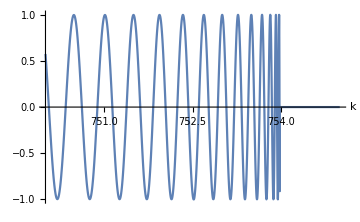

```mathematica
With[{zs=0.5,zr=0.6,ω=2Pi 300+0I},
{
Plot[
Im@stackRefExperiment2[ω,k/ω,model, dList,{zs,zr}][[1,1]],{k,750,755},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium]
}
]
```

```mathematica
With[{ω=2Pi 1,k=1,zs=.1,zr=.2},stackRefExperiment2[ω,k/ω,model, dList,{zs,zr}][[1,1]]]
```

0.298632+0.0700162 ⅈ

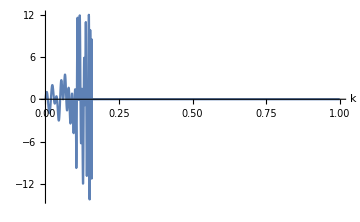
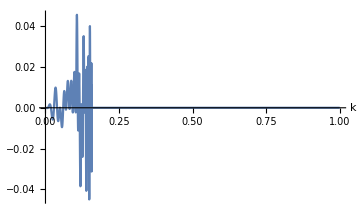

```mathematica
With[{x=0.3,zs=0.1,zr=.3,ω=2Pi 50+0I},
{
Plot[
Re@integrandk[x,k ,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{k,0,1},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium],
Plot[
Re@integrandkFullDisp[x,k ,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr,{1,1}],{k,0,1},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium]
}
]
```

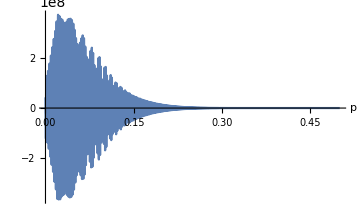
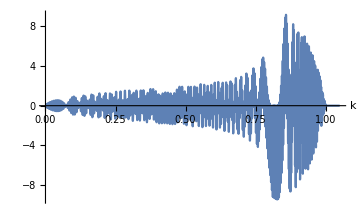

```mathematica
With[{x=1,zs=0.4,zr=0.3,ω=2Pi 400},
{
Plot[
Im@integrandp[x,p+.005I,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{p,0,.5},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium],
Plot[
Im@integrandk[x,k ,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{k,0,1.05},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium]
}
]
```

```mathematica
With[{x=1,zs=.1,zr=.2},
integrateNow[10,x,{zs,zr},200,model,dList,ω0,{.1,.6}]
]
```

-0.00248925-0.00928332 ⅈ

### Numerical testing: compute single trace

```mathematica
deltafreq=1;
maxfreq=400;
freqvec=Table[f,{f,1,maxfreq,deltafreq}];
fricker=30;
```

```mathematica
With[{x=1,zs=.4,zr=.3,fmax=maxfreq},
{singleTrace,srcF}=Transpose[
ParallelTable[{Quiet@integrateNow[freqvec[[i]],x,{zs,zr},fmax,model,dList,ω0,{.05,1.1}],rickerF[freqvec[[i]],fricker]},{i,1,Length@freqvec}]]
];
```

```mathematica
Export[NotebookDirectory[]<>"x_1KM.mc",Compress[{singleTrace,srcF}],"String"];
```

```mathematica
(*data=Uncompress@Import[NotebookDirectory[]<>"x_5KM.mc","String"];*)
```

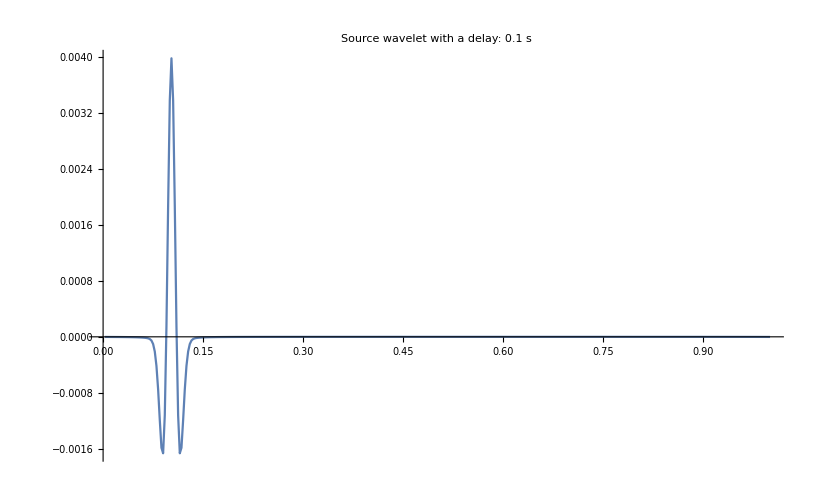

```mathematica
(*time vector*)
t=Range[Length[srcF]]/(deltafreq Length[srcF])//N;

With[{delay=.1},
ListLinePlot[{t,Re@InverseFourier@(srcF (Exp[ⅈ 2Pi# delay]&/@(freqvec-1)))}ᵀ,PlotRange->{Automatic,Full},PlotLabel->"Source wavelet with a delay: "<>ToString[delay]<>" s"]
]
```

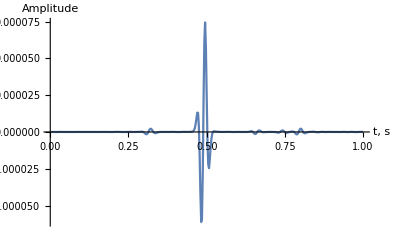

```mathematica
ListLinePlot[{t,Re@InverseFourier@(singleTrace srcF)}ᵀ,PlotRange->Full,AxesLabel->{"t, s","Amplitude"}]
```

```mathematica
Join[singleTrace,Conjugate[singleTrace]]//Dimensions
```

{800}

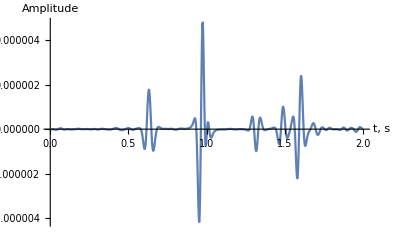

```mathematica
ListLinePlot[{Range[2Length[srcF]]/(deltafreq Length[srcF]),Re@InverseFourier@(
Join[singleTrace,Conjugate[singleTrace]//Reverse]
Join[srcF,Conjugate[srcF]//Reverse]
)
}ᵀ,PlotRange->Full,AxesLabel->{"t, s","Amplitude"}]
```

```mathematica
gather=Table[
With[{x=x0,zs=.4,zr=.3,fmax=maxfreq},

ParallelTable[Quiet@integrateNow[freqvec[[i]],x,{zs,zr},fmax,model,dList,ω0,{.05,1.1}],{i,1,Length@freqvec}]

],
{x0,0,5,.025}
]ᵀ;
```

```mathematica
Export[NotebookDirectory[]<>"x0-5KM_dx25M_T2.mc",Compress[gather],"String"]
```

```mathematica
gather=Uncompress@Import[NotebookDirectory[]<>"x0-5KM_dx25M.mc","String"];
```

```mathematica
xvec=Table[x0,{x0,0,5,.025}];
```

```mathematica
csg=Re@InverseFourier@(
Join[gather,Conjugate[gather]//Reverse]
Join[srcF,Conjugate[srcF]//Reverse]
);
```

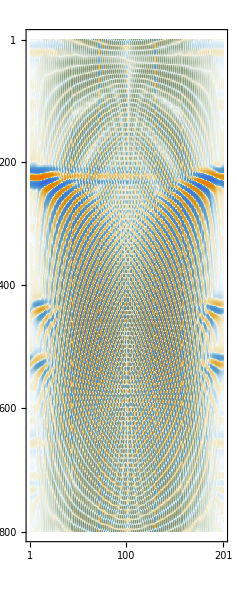

```mathematica
MatrixPlot[csg]
```

### Numerical testing: compute single trace: Ivan’s model

```mathematica
modelIvan={
{vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den,50000,50000}/.vp->2.0002/.vs->1.0002/.den->2.0002,
{vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den,50000,50000}/.vp->3.0002/.vs->1.5002/.den->3.0002};
```

```mathematica
deltafreq=.5;
maxfreq=50;
freqvec=Table[f,{f,0,maxfreq,deltafreq}];
fricker=10;
```

```mathematica
srcF=rickerF[#,fricker]&/@freqvec;
```

```mathematica
With[{x=.3,zs=.1,zr=.4,fmax=maxfreq},
singleTrace=
ParallelTable[Quiet@integrateNowFullDisp[freqvec[[i]],x,{zs,zr},fmax,model,dList,ω0,{.1,.2},{1,1}],{i,2,Length@freqvec}]];
```

```mathematica
trace=Join[{0},singleTrace];
```

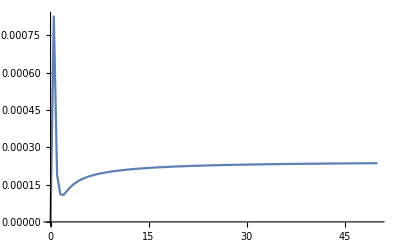

```mathematica
ListLinePlot[{freqvec,Abs@trace}ᵀ,PlotRange->Full
]
```

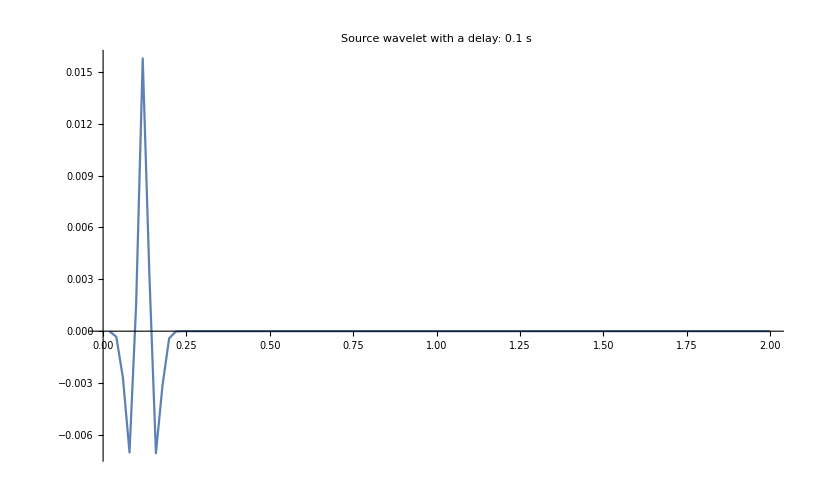

```mathematica
(*time vector*)
t=Range[Length[srcF]]/(deltafreq Length[srcF])//N;

With[{delay=.1},
ListLinePlot[{t,Re@InverseFourier@(srcF (Exp[ⅈ 2Pi# delay]&/@freqvec))}ᵀ,PlotRange->{Automatic,Full},PlotLabel->"Source wavelet with a delay: "<>ToString[delay]<>" s"]
]
```

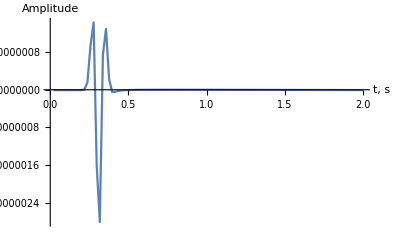

```mathematica
ListLinePlot[{t,Re@InverseFourier@(trace srcF)}ᵀ,PlotRange->Full,AxesLabel->{"t, s","Amplitude"}]
```

```mathematica
Join[singleTrace,Conjugate[singleTrace]]//Dimensions
```

{800}

```mathematica
ListLinePlot[{Range[2Length[srcF]]/(deltafreq Length[srcF]),Re@InverseFourier@(
Join[singleTrace,Conjugate[singleTrace]//Reverse]
Join[srcF,Conjugate[srcF]//Reverse]
)
}ᵀ,PlotRange->Full,AxesLabel->{"t, s","Amplitude"}]
```

Thread::tdlen: Objects of unequal length in {0.000211546+0.000798494 ⅈ,0.000110476+0.000154258 ⅈ,0.0000603157+0.0000928762 ⅈ,0.0000334351+0.000103324 ⅈ,«43»,-0.000225956+0.0000212601 ⅈ,-0.000154655-0.000166587 ⅈ,0.0000380813-0.000224442 ⅈ,«150»} {«1»} cannot be combined.

InverseFourier::fftl: Argument {0.000211546+0.000798494 ⅈ,0.000110476+0.000154258 ⅈ,0.0000603157+0.0000928762 ⅈ,0.0000334351+0.000103324 ⅈ,«43»,-0.000225956+0.0000212601 ⅈ,-0.000154655-0.000166587 ⅈ,0.0000380813-0.000224442 ⅈ,«150»} {«1»} is not a non-empty list or rectangular array of numeric quantities.

Transpose::nmtx: The first two levels of {{0.019802,0.039604,0.0594059,0.0792079,0.0990099,0.118812,0.138614,0.158416,0.178218,«33»,0.851485,0.871287,0.891089,0.910891,0.930693,0.950495,0.970297,0.990099,«152»},Re[«1»]} cannot be transposed.

ListLinePlot::lpn: Transpose[{{0.019802,0.039604,0.0594059,0.0792079,0.0990099,0.118812,0.138614,0.158416,«35»,0.871287,0.891089,0.910891,0.930693,0.950495,0.970297,0.990099,«152»},Re[InverseFourier[{«1»} {«1»}]]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[Transpose[{{0.019802,0.039604,0.0594059,0.0792079,0.0990099,0.118812,0.138614,0.158416,0.178218,0.19802,0.217822,0.237624,0.257426,0.277228,0.29703,0.316832,0.336634,0.356436,0.376238,0.39604,0.415842,0.435644,0.455446,0.475248,0.49505,0.514851,0.534653,0.554455,0.574257,0.594059,0.613861,0.633663,0.653465,0.673267,0.693069,0.712871,0.732673,0.752475,0.772277,0.792079,0.811881,0.831683,0.851485,0.871287,0.891089,0.910891,0.930693,0.950495,0.970297,0.990099,1.0099,1.0297,1.0495,1.06931,1.08911,1.10891,1.12871,1.14851,1.16832,1.18812,1.20792,1.22772,1.24752,1.26733,1.28713,1.30693,1.32673,1.34653,1.36634,1.38614,1.40594,1.42574,1.44554,1.46535,1.48515,1.50495,1.52475,1.54455,1.56436,1.58416,1.60396,1.62376,1.64356,1.66337,1.68317,1.70297,1.72277,1.74257,1.76238,1.78218,1.80198,1.82178,1.84158,1.86139,1.88119,1.90099,1.92079,1.94059,1.9604,1.9802,2.,2.0198,2.0396,2.05941,2.07921,2.09901,2.11881,2.13861,2.15842,2.17822,2.19802,2.21782,2.23762,2.25743,2.27723,2.29703,2.31683,2.33663,2.35644,2.37624,2.39604,2.41584,2.43564,2.45545,2.47525,2.49505,2.51485,2.53465,2.55446,2.57426,2.59406,2.61386,2.63366,2.65347,2.67327,2.69307,2.71287,2.73267,2.75248,2.77228,2.79208,2.81188,2.83168,2.85149,2.87129,2.89109,2.91089,2.93069,2.9505,2.9703,2.9901,3.0099,3.0297,3.0495,3.06931,3.08911,3.10891,3.12871,3.14851,3.16832,3.18812,3.20792,3.22772,3.24752,3.26733,3.28713,3.30693,3.32673,3.34653,3.36634,3.38614,3.40594,3.42574,3.44554,3.46535,3.48515,3.50495,3.52475,3.54455,3.56436,3.58416,3.60396,3.62376,3.64356,3.66337,3.68317,3.70297,3.72277,3.74257,3.76238,3.78218,3.80198,3.82178,3.84158,3.86139,3.88119,3.90099,3.92079,3.94059,3.9604,3.9802,4.},Re[InverseFourier[{0.000211546+0.000798494 ⅈ,0.000110476+0.000154258 ⅈ,0.0000603157+0.0000928762 ⅈ,0.0000334351+0.000103324 ⅈ,-0.0000336977+0.00011937 ⅈ,-0.000118794+0.0000719732 ⅈ,-0.000145092-0.0000412736 ⅈ,-0.0000678651-0.000145236 ⅈ,0.00007129-0.000152031 ⅈ,0.00016895-0.000042278 ⅈ,0.000142873+0.000108473 ⅈ,3.99556×10^-6+0.000183792 ⅈ,-0.00014484+0.000119353 ⅈ,-0.000186572-0.0000410847 ⅈ,-0.0000837011-0.000175029 ⅈ,0.0000879159-0.000175915 ⅈ,0.000195205-0.0000388806 ⅈ,0.000151905+0.000131916 ⅈ,-0.0000115233+0.000202817 ⅈ,-0.000169027+0.000115874 ⅈ,-0.000196557-0.0000635382 ⅈ,-0.0000701995-0.000195884 ⅈ,0.00011309-0.000176332 ⅈ,0.000210003-0.0000180736 ⅈ,0.00014321+0.000156299 ⅈ,-0.0000367715+0.000209917 ⅈ,-0.000189761+0.0000992914 ⅈ,-0.000195264-0.0000903559 ⅈ,-0.000047537-0.000210792 ⅈ,0.000138755-0.00016679 ⅈ,0.00021762+8.47093×10^-6 ⅈ,0.000126282+0.00017839 ⅈ,-0.0000647968+0.00020951 ⅈ,-0.000206295+0.0000764357 ⅈ,-0.000186813-0.000117443 ⅈ,-0.0000206501-0.000220327 ⅈ,0.000162643-0.000150941 ⅈ,0.000219327+0.0000372172 ⅈ,0.000104263+0.000197132 ⅈ,-0.0000931285+0.000203201 ⅈ,-0.000218385+0.0000499364 ⅈ,-0.00017293-0.000143156 ⅈ,8.31509×10^-6-0.000224796 ⅈ,0.00018376-0.000130501 ⅈ,0.000215797+0.0000664685 ⅈ,0.0000787697+0.000212043 ⅈ,-0.000120483+0.000191897 ⅈ,-0.000225956+0.0000212601 ⅈ,-0.000154655-0.000166587 ⅈ,0.0000380813-0.000224442 ⅈ,0.00020154-0.000106564 ⅈ,0.000207516+0.0000951616 ⅈ,0.0000508881+0.000222864 ⅈ,-0.000146027+0.000176263 ⅈ,-0.000229017-8.57006×10^-6 ⅈ,-0.000132768-0.000187138 ⅈ,0.0000677298-0.000219504 ⅈ,0.000215619-0.0000799722 ⅈ,0.000194911+0.000122516 ⅈ,0.0000214699+0.000229455 ⅈ,-0.000169144+0.000156869 ⅈ,-0.00022764-0.0000387387 ⅈ,-0.000107942-0.000204376 ⅈ,0.0000965235-0.000210241 ⅈ,0.000225755-0.0000514511 ⅈ,0.0001784+0.00014791 ⅈ,-8.7505×10^-6+0.000231767 ⅈ,-0.000189352+0.000134256 ⅈ,-0.000221955-0.0000685461 ⅈ,-0.0000807985-0.00021798 ⅈ,0.000123837-0.000196945 ⅈ,0.000231798-0.0000216654 ⅈ,0.000158411+0.000170823 ⅈ,-0.000039109+0.000229821 ⅈ,-0.000206268+0.000108956 ⅈ,-0.000212146-0.0000973695 ⅈ,-0.0000519391-0.00022772 ⅈ,0.000149125-0.000179947 ⅈ,0.00023368+8.75737×10^-6 ⅈ,0.000135394+0.000190822 ⅈ,-0.0000689916+0.000223708 ⅈ,-0.000219592+0.0000815078 ⅈ,-0.000198456-0.000124647 ⅈ,-0.0000219514-0.000233443 ⅈ,0.000171913-0.000159619 ⅈ,0.000231403+0.0000392179 ⅈ,0.000109825+0.000207547 ⅈ,-0.0000978265+0.000213584 ⅈ,-0.000229098+0.0000524558 ⅈ,-0.000181176-0.00014987 ⅈ,8.58646×10^-6-0.000235073 ⅈ,0.000191788-0.000136369 ⅈ,0.000225041+0.0000691429 ⅈ,0.0000821998+0.000220707 ⅈ,-0.000125083+0.000199664 ⅈ,-0.000234635+0.0000223501 ⅈ,-0.00016065-0.000172586 ⅈ,0.0000391078-0.000232605 ⅈ,0.000208404-0.000110642 ⅈ,0.000214734+0.0000979873 ⅈ,0.000214734-0.0000979873 ⅈ,0.000208404+0.000110642 ⅈ,0.0000391078+0.000232605 ⅈ,-0.00016065+0.000172586 ⅈ,-0.000234635-0.0000223501 ⅈ,-0.000125083-0.000199664 ⅈ,0.0000821998-0.000220707 ⅈ,0.000225041-0.0000691429 ⅈ,0.000191788+0.000136369 ⅈ,8.58646×10^-6+0.000235073 ⅈ,-0.000181176+0.00014987 ⅈ,-0.000229098-0.0000524558 ⅈ,-0.0000978265-0.000213584 ⅈ,0.000109825-0.000207547 ⅈ,0.000231403-0.0000392179 ⅈ,0.000171913+0.000159619 ⅈ,-0.0000219514+0.000233443 ⅈ,-0.000198456+0.000124647 ⅈ,-0.000219592-0.0000815078 ⅈ,-0.0000689916-0.000223708 ⅈ,0.000135394-0.000190822 ⅈ,0.00023368-8.75737×10^-6 ⅈ,0.000149125+0.000179947 ⅈ,-0.0000519391+0.00022772 ⅈ,-0.000212146+0.0000973695 ⅈ,-0.000206268-0.000108956 ⅈ,-0.000039109-0.000229821 ⅈ,0.000158411-0.000170823 ⅈ,0.000231798+0.0000216654 ⅈ,0.000123837+0.000196945 ⅈ,-0.0000807985+0.00021798 ⅈ,-0.000221955+0.0000685461 ⅈ,-0.000189352-0.000134256 ⅈ,-8.7505×10^-6-0.000231767 ⅈ,0.0001784-0.00014791 ⅈ,0.000225755+0.0000514511 ⅈ,0.0000965235+0.000210241 ⅈ,-0.000107942+0.000204376 ⅈ,-0.00022764+0.0000387387 ⅈ,-0.000169144-0.000156869 ⅈ,0.0000214699-0.000229455 ⅈ,0.000194911-0.000122516 ⅈ,0.000215619+0.0000799722 ⅈ,0.0000677298+0.000219504 ⅈ,-0.000132768+0.000187138 ⅈ,-0.000229017+8.57006×10^-6 ⅈ,-0.000146027-0.000176263 ⅈ,0.0000508881-0.000222864 ⅈ,0.000207516-0.0000951616 ⅈ,0.00020154+0.000106564 ⅈ,0.0000380813+0.000224442 ⅈ,-0.000154655+0.000166587 ⅈ,-0.000225956-0.0000212601 ⅈ,-0.000120483-0.000191897 ⅈ,0.0000787697-0.000212043 ⅈ,0.000215797-0.0000664685 ⅈ,0.00018376+0.000130501 ⅈ,8.31509×10^-6+0.000224796 ⅈ,-0.00017293+0.000143156 ⅈ,-0.000218385-0.0000499364 ⅈ,-0.0000931285-0.000203201 ⅈ,0.000104263-0.000197132 ⅈ,0.000219327-0.0000372172 ⅈ,0.000162643+0.000150941 ⅈ,-0.0000206501+0.000220327 ⅈ,-0.000186813+0.000117443 ⅈ,-0.000206295-0.0000764357 ⅈ,-0.0000647968-0.00020951 ⅈ,0.000126282-0.00017839 ⅈ,0.00021762-8.47093×10^-6 ⅈ,0.000138755+0.00016679 ⅈ,-0.000047537+0.000210792 ⅈ,-0.000195264+0.0000903559 ⅈ,-0.000189761-0.0000992914 ⅈ,-0.0000367715-0.000209917 ⅈ,0.00014321-0.000156299 ⅈ,0.000210003+0.0000180736 ⅈ,0.00011309+0.000176332 ⅈ,-0.0000701995+0.000195884 ⅈ,-0.000196557+0.0000635382 ⅈ,-0.000169027-0.000115874 ⅈ,-0.0000115233-0.000202817 ⅈ,0.000151905-0.000131916 ⅈ,0.000195205+0.0000388806 ⅈ,0.0000879159+0.000175915 ⅈ,-0.0000837011+0.000175029 ⅈ,-0.000186572+0.0000410847 ⅈ,-0.00014484-0.000119353 ⅈ,3.99556×10^-6-0.000183792 ⅈ,0.000142873-0.000108473 ⅈ,0.00016895+0.000042278 ⅈ,0.00007129+0.000152031 ⅈ,-0.0000678651+0.000145236 ⅈ,-0.000145092+0.0000412736 ⅈ,-0.000118794-0.0000719732 ⅈ,-0.0000336977-0.00011937 ⅈ,0.0000334351-0.000103324 ⅈ,0.0000603157-0.0000928762 ⅈ,0.000110476-0.000154258 ⅈ,0.000211546-0.000798494 ⅈ} {0.,0.0000447847,0.0001778,0.000395081,0.000690182,0.00105442,0.00147717,0.0019463,0.00244854,0.00296999,0.00349656,0.00401445,0.00451057,0.00497293,0.00539097,0.00575582,0.00606048,0.00629992,0.00647115,0.00657312,0.00660664,0.00657422,0.00647984,0.00632873,0.00612708,0.0058818,0.00560021,0.00528982,0.00495809,0.00461219,0.00425888,0.00390433,0.00355403,0.00321275,0.00288444,0.00257232,0.0022788,0.00200561,0.0017538,0.00152384,0.0013157,0.00112891,0.000962665,0.000815879,0.000687282,0.000575472,0.000478975,0.000396296,0.000325958,0.000266535,0.000216678,0.000175128,0.000140731,0.000112443,0.0000893297,0.0000705649,0.0000554271,0.000043292,0.0000336244,0.00002597,0.0000199465,0.0000152353,0.0000115725,8.74197×10^-6,6.56749×10^-6,4.90689×10^-6,3.64616×10^-6,2.6946×10^-6,1.98056×10^-6,1.44785×10^-6,1.0527×10^-6,7.61265×10^-7,5.4755×10^-7,3.91717×10^-7,2.78732×10^-7,1.97275×10^-7,1.38877×10^-7,9.72449×10^-8,6.77307×10^-8,4.69234×10^-8,3.23358×10^-8,2.21651×10^-8,1.51131×10^-8,1.02503×10^-8,6.91543×10^-9,4.64097×10^-9,3.09818×10^-9,2.05739×10^-9,1.35906×10^-9,8.93056×10^-10,5.83764×10^-10,3.79591×10^-10,2.45539×10^-10,1.57997×10^-10,1.01136×10^-10,6.44011×10^-11,4.07956×10^-11,2.57079×10^-11,1.6116×10^-11,1.00504×10^-11,6.23524×10^-12,6.23524×10^-12,1.00504×10^-11,1.6116×10^-11,2.57079×10^-11,4.07956×10^-11,6.44011×10^-11,1.01136×10^-10,1.57997×10^-10,2.45539×10^-10,3.79591×10^-10,5.83764×10^-10,8.93056×10^-10,1.35906×10^-9,2.05739×10^-9,3.09818×10^-9,4.64097×10^-9,6.91543×10^-9,1.02503×10^-8,1.51131×10^-8,2.21651×10^-8,3.23358×10^-8,4.69234×10^-8,6.77307×10^-8,9.72449×10^-8,1.38877×10^-7,1.97275×10^-7,2.78732×10^-7,3.91717×10^-7,5.4755×10^-7,7.61265×10^-7,1.0527×10^-6,1.44785×10^-6,1.98056×10^-6,2.6946×10^-6,3.64616×10^-6,4.90689×10^-6,6.56749×10^-6,8.74197×10^-6,0.0000115725,0.0000152353,0.0000199465,0.00002597,0.0000336244,0.000043292,0.0000554271,0.0000705649,0.0000893297,0.000112443,0.000140731,0.000175128,0.000216678,0.000266535,0.000325958,0.000396296,0.000478975,0.000575472,0.000687282,0.000815879,0.000962665,0.00112891,0.0013157,0.00152384,0.0017538,0.00200561,0.0022788,0.00257232,0.00288444,0.00321275,0.00355403,0.00390433,0.00425888,0.00461219,0.00495809,0.00528982,0.00560021,0.0058818,0.00612708,0.00632873,0.00647984,0.00657422,0.00660664,0.00657312,0.00647115,0.00629992,0.00606048,0.00575582,0.00539097,0.00497293,0.00451057,0.00401445,0.00349656,0.00296999,0.00244854,0.0019463,0.00147717,0.00105442,0.000690182,0.000395081,0.0001778,0.0000447847,0.}]]}],PlotRange→Full,AxesLabel→{t, s,Amplitude}]

### Numerical testing: compute single trace: Ivan’s model using ThinLayer package

```mathematica
modelIvan={
{vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den}/.vp->2.0002/.vs->1.0002/.den->2.0002,
{vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den}/.vp->3.0002/.vs->1.5002/.den->3.0002};
```

```mathematica
<<ThinLayer`
```

```mathematica
tlSetLayer[1,modelIvan[[1]]]
tlSetLayer[2,modelIvan[[2]]]
```

{8.0024,4.0004,8.0024,2.001,2.0002}

{27.0054,13.5009,27.0054,6.75225,3.0002}

```mathematica
Module[{ωList,noffsets,scaling,layers,thicknesses,kList,ϕ,ref,dHT,zs,zr,calclist},zs=.1;zr=.4;
layers={1,2};
thicknesses={1,1};
ωList=2Pi Range[.5,50.,.5];
noffsets=1;
scaling=1;
kList=Range[0,1,.001];
ref[ω_,k_]:=(DiagonalMatrix[E^(I ω tlQLmatrices[1,k/ω][[1]] zs)].tlReflectivity[layers,thicknesses,k/ω,ω].DiagonalMatrix[E^(I ω tlQLmatrices[1,k/ω][[1]] zr)])[[1,1]];
ref[ω_,k_?VectorQ]:=ref[ω,#]&/@k;
dHT=tlDiscreteHankelTransform[#1,0.,#2]&;
AbsoluteTiming[test=ref[#,kList]&/@ωList;
test2=tlDiscreteHankelTransform[#1,0.,5]&/@test;]
]
```

{815.551,Null}

```mathematica
test2[[;;,3,1]]
```

{0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ,0.275457+0. ⅈ}

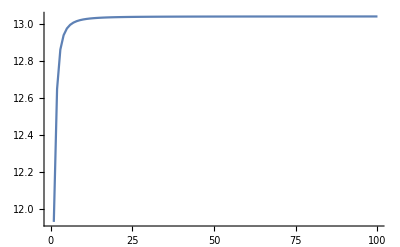

```mathematica
ListLinePlot[Abs@test2[[;;,1,2]],PlotRange->Full]
```

```mathematica
rickerSpectrum[w_,wp_]=(2 w^2)/(Sqrt[π] wp^3) Exp[-(w^2/wp^2)];
```

```mathematica
fset=Module[{resamp,tSamp=1024,sampRate=1/512,maxω,δω,offSamp=400},resamp=ArrayResample[test2,{tSamp,offSamp}];
maxω=1024;
δω=maxω/tSamp;
Table[RotateRight[InverseFourier[RotateLeft[tSamp rickerSpectrum[Range[-N@maxω,N@maxω,δω],2 π 30] (Reverse@Conjugate@resamp[[;;,i,2]])~Join~{1.+0. I}~Join~resamp[[;;,i,2]],tSamp],FourierParameters->{1,-1}],tSamp],{i,1,offSamp}]];
```

```mathematica
deltafreq=.5;
maxfreq=50;
freqvec=Table[f,{f,0,maxfreq,deltafreq}];
fricker=10;
```

```mathematica
srcF=rickerF[#,fricker]&/@freqvec;
```

```mathematica
With[{x=.3,zs=.1,zr=.4,fmax=maxfreq},
singleTrace=
ParallelTable[Quiet@integrateNowFullDisp[freqvec[[i]],x,{zs,zr},fmax,model,dList,ω0,{.1,.2},{1,1}],{i,2,Length@freqvec}]];
```

```mathematica
trace=Join[{0},singleTrace];
```

```mathematica
ListLinePlot[{freqvec,Abs@trace}ᵀ,PlotRange->Full
]
```

-Graphics-

```mathematica
(*time vector*)
t=Range[Length[srcF]]/(deltafreq Length[srcF])//N;

With[{delay=.1},
ListLinePlot[{t,Re@InverseFourier@(srcF (Exp[ⅈ 2Pi# delay]&/@freqvec))}ᵀ,PlotRange->{Automatic,Full},PlotLabel->"Source wavelet with a delay: "<>ToString[delay]<>" s"]
]
```

-Graphics-

```mathematica
ListLinePlot[{t,Re@InverseFourier@(trace srcF)}ᵀ,PlotRange->Full,AxesLabel->{"t, s","Amplitude"}]
```

-Graphics-

```mathematica
Join[singleTrace,Conjugate[singleTrace]]//Dimensions
```

{800}